## Init data

```mathematica
MinV = 1000;

TargetF:=2*Pi*x1*x2+2*Pi*x1^2;
```

### Used formulas

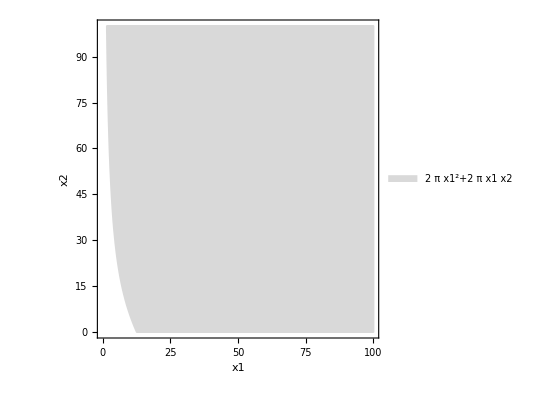

{4 π x1+2 π x2,2 π x1}

200 √10 π

2 π (1-λ)^2+2 π (1-λ) (2-λ)

```mathematica
EvaluateTargetF[x1_, x2_]:=2*Pi*x1*x2+2*Pi*x1^2;

GradTargetF:=Grad[TargetF, {x1,x2}];
EvaluateGradTarget1[value1_, value2_]:=Assuming[{x1==value1, x2==value2},Refine[GradTargetF[[1]]]];
EvaluateGradTarget2[value1_, value2_]:=Assuming[{x1==value1, x2==value2},Refine[GradTargetF[[2]]]];
AbsGradF[x1_,x2_]:=Sqrt[EvaluateGradTarget1[x1, x2]^2+EvaluateGradTarget2[x1, x2]^2];

PlotRestrictionArea[max1_,max2_]:=RegionPlot[TargetF≥MinV,{x1,0,max1},{x2,0,max2},PlotLegends->{TargetF}, AxesLabel->Automatic, PlotStyle->LightGray,BoundaryStyle->LightGray]
PlotRestrictionArea[100, 100]
Print[GradTargetF]
Print[AbsGradF[100, 100]]
EvaluateTargetF[1-λ, 2-λ]
```

### Output functions

```mathematica
PlotAllowedPoints[x1_,x2_]:=Module[{i=0,j=0,array = {{0,0}}},
For[i=0,i≤x1,i++,
For[j=0,j≤x2,j++,
AppendTo[array,{i,j}];
];
];
ListPlot[array, PlotStyle->Black]
];

PlotRestrictionArea[max1_,max2_]:=RegionPlot[QRestriction≤q0,{x1,0,max1},{x2,0,max2},PlotLegends->{QRestriction}, AxesLabel->Automatic, PlotStyle->LightGray,BoundaryStyle->LightGray];

PlotAllowedArea[max1_,max2_]:=Show[PlotRestrictionArea[max1,max2],PlotAllowedPoints[max1,max2]];

PointsLength[x1_,y1_,x2_,y2_]:=Sqrt[(x2-x1)^2+(y2-y1)^2];

PrintResult[k_,init1_,init2_, x1_,x2_]:=Module[{ceil1=Ceiling[x1],ceil2=Ceiling[x2],floor1=Floor[x1],floor2=Floor[x2],ans1=-1,ans2=-1},
Module[{p1,p2,p3,p4,l, ansL},
p1={ceil1,ceil2};
p2:={ceil1,floor2};
p3:={floor1,floor2};
p4={floor1,ceil1};
l:={PointsLength[x1,x2,p1[[1]],p1[[2]]],PointsLength[x1,x2,p2[[1]],p2[[2]]],PointsLength[x1,x2,p3[[1]],p3[[2]]],PointsLength[x1,x2,p4[[1]],p4[[2]]]};
ansL=l[[1]];
If[EvaluateRestriction[p1[[1]], p1[[2]]]≤q0,
ans1=p1[[1]];
ans2=p1[[2]];,
If[EvaluateRestriction[p2[[1]], p2[[2]]]≤q0&&l[[2]]<ansL,
ansL=l[[2]];
ans1=p2[[1]];
ans2=p2[[2]];,
If[EvaluateRestriction[p3[[1]], p3[[2]]]≤q0&&l[[3]]<ansL,
ansL=l[[3]];
ans1=p3[[1]];
ans2=p3[[2]];,
If[EvaluateRestriction[p4[[1]], p4[[2]]]≤q0&&l[[4]]<ansL,
ansL=l[[4]];
ans1=p4[[1]];
ans2=p4[[2]];
];
];
];
];
];
Print[Row[{"Iterations",k},"="]];
Print[Row[{"Init 1st block",Row[{1,init1},"+"]},"="]];
Print[Row[{"init 2nd block",Row[{1,init2},"+"]},"="]];
If[ans1==-1||ans2==-1,Print["Failed"],
Print[Row[{"Add to 1st block",x1-init1},"="]];
Print[Row[{"Add to 2nd block",x2-init2},"="]];
Print[Row[{"Solution for 1st block",Row[{x1,ans1},"→"]},"="]];
Print[Row[{"Solution for 2nd block",Row[{x2,ans2},"→"]},"="]];
Print[Row[{"Probability of failure",EvaluateRestriction[ans1,ans2]},"="]];
Print[Row[{"Power consumption",EvaluateTargetF[ans1,ans2]},"="]];];
];
```

## Plots

### Plotting functions

```mathematica
FindMinSplit[init1_,init2_,ϵ_]:=Module[{k=1,cur1=init1,cur2=init2,array,func, grad1, grad2,minL},
array={{init1,init2}};
While[AbsGradF[cur1,cur2]≥ϵ,
grad1=EvaluateGradTarget1[cur1,cur2];
grad2=EvaluateGradTarget2[cur1,cur2];
func=EvaluateTargetF[cur1-grad1*λ, cur2-grad2*λ];
minL=λ/.Last[FindMinimum[func,{λ,0}]];
cur1=cur1-grad1*minL;
cur2=cur2-grad2*minL;
AppendTo[array,{cur1,cur2}];
];
];
FindMinSplit[100,100,0.001]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::nrnum: The function value False is not a real number at {λ} = {-136664.}.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

### Plots

```mathematica
λ=0.05;
ϵ=0.00005;
```

#### Старт из области, где выполняется ограничение

```mathematica
FindMinSplit[3,3,λ,ϵ]
```

==Iterations116

==Init 1st block++13

==init 2nd block++13

==Add to 1st block-1.49861

==Add to 2nd block-2.49097

==Solution for 1st block→→1.501392

==Solution for 2nd block→→0.5090351

==Probability of failure0.000525

==Power consumption19

-Graphics-

```mathematica
FindMinSplit[2,2,λ,ϵ]
```

==Iterations19

==Init 1st block++12

==init 2nd block++12

==Add to 1st block-0.749069

==Add to 2nd block-1.24891

==Solution for 1st block→→1.250932

==Solution for 2nd block→→0.7510941

==Probability of failure0.000525

==Power consumption19

-Graphics-

```mathematica
FindMinSplit[2,1,λ,ϵ]
```

==Iterations114

==Init 1st block++12

==init 2nd block++11

==Add to 1st block-0.299106

==Add to 2nd block-0.489447

==Solution for 1st block→→1.700892

==Solution for 2nd block→→0.5105531

==Probability of failure0.000525

==Power consumption19

-Graphics-

#### Старт из области где не выполняется ограничение

```mathematica
FindMinSplit[0,0,λ,ϵ]
```

==Iterations2284

==Init 1st block++10

==init 2nd block++10

Failed

-Graphics-

```mathematica
FindMinSplit[0,1,λ,ϵ]
```

==Iterations2284

==Init 1st block++10

==init 2nd block++11

Failed

-Graphics-

```mathematica
FindMinSplit[1,0,λ,ϵ]
```

==Iterations1361

==Init 1st block++11

==init 2nd block++10

==Add to 1st block0.0263738

==Add to 2nd block0.192365

==Solution for 1st block→→1.026372

==Solution for 2nd block→→0.1923651

==Probability of failure0.000525

==Power consumption19

-Graphics-